## Import Utils

```mathematica
Get["D:\\Documents\\workspace\\课题\\workspace\\Local\\Public\\mathematica\\PN_inverse\\InversePNUtils.nb"];
```

```mathematica
(*NotebookEvaluate["D:\\Documents\\workspace\\课题\\PN_inverse\\InversePNUtils.nb"]*)
```

```mathematica
NotebookEvaluate["D:\\Documents\\workspace\\课题\\workspace\\Local\\Public\\mathematica\\PN_inverse\\InversePNUtils.nb"]
```

## 设置non-GR参数字符flag

```mathematica
eventFlag="GW150914";
psiFlag="psi";
alphaFlag="alpha";

deviationFlag="fdchi";
deviationOrder=4;
deviationType="fractional";

alphaName=alphaFlag<>ToString[deviationOrder]
psiName=psiFlag<>ToString[deviationOrder]
deviationName=deviationFlag<>ToString[deviationOrder]
modifiedAlphaName=alphaFlag<>ToString[deviationOrder]<>deviationFlag
modifiedPsiName=psiFlag<>ToString[deviationOrder]<>deviationFlag
```

alpha4

psi4

fdchi4

alpha4fdchi

psi4fdchi

## Prepare Data from CSV or HDF

```mathematica
csvFolder="D:\\Documents\\workspace\\课题\\workspace\\Local\\Parameterized_PN_Tests\\csv"<>"\\"<>eventFlag
csvName="OGC4-GW150914_"<>deviationName<>".csv"
csvPath=csvFolder<>"\\"<>csvName
```

D:\Documents\workspace\课题\workspace\Local\Parameterized_PN_Tests\csv\GW150914

OGC4-GW150914_fdchi4.csv

D:\Documents\workspace\课题\workspace\Local\Parameterized_PN_Tests\csv\GW150914\OGC4-GW150914_fdchi4.csv

### from CSV

```mathematica
CSVSamples=Import[csvPath];

samples=<||>;
samples["mass1"]=CSVSamples[[All,1]][[2;;]];
samples["mass2"]=CSVSamples[[All,2]][[2;;]];
samples["spin1_z"]=CSVSamples[[All,3]][[2;;]];
samples["spin2_z"]=CSVSamples[[All,4]][[2;;]];
samples["eta"]=CSVSamples[[All,5]][[2;;]];
samples["Mchirp"]=CSVSamples[[All,6]][[2;;]];
samples[deviationName]=CSVSamples[[All,7]][[2;;]];
```

```mathematica
samples["chis"]=χs[samples["spin1_z"],samples["spin2_z"]];
samples["chia"]=χa[samples["spin1_z"],samples["spin2_z"]];
```

### Calculate Coefficients

#### N-Order Coefficients, α

```mathematica
samples["alpha2"]=MapThread[
Alpha[2,η[#1,#2],#3,#4]&,
{samples["mass1"],samples["mass2"],samples["spin1_z"],samples["spin2_z"]}
];

samples["alpha3"]=MapThread[
Alpha[3,η[#1,#2],#3,#4]&,
{samples["mass1"],samples["mass2"],samples["spin1_z"],samples["spin2_z"]}
];

samples["alpha4"]=MapThread[
Alpha[4,η[#1,#2],#3,#4]&,
{samples["mass1"],samples["mass2"],samples["spin1_z"],samples["spin2_z"]}
];
samples["alpha6"]=MapThread[
Alpha[6,η[#1,#2],#3,#4]&,
{samples["mass1"],samples["mass2"],samples["spin1_z"],samples["spin2_z"]}
];
samples["alpha7"]=MapThread[
Alpha[7,η[#1,#2],#3,#4]&,
{samples["mass1"],samples["mass2"],samples["spin1_z"],samples["spin2_z"]}
];
```

#### N-Order Log Coefficients, α

```mathematica
samples["alpha5l"]=MapThread[
Alpha["5l",η[#1,#2],#3,#4]&,
{samples["mass1"],samples["mass2"],samples["spin1_z"],samples["spin2_z"]}
];
samples["alpha6l"]=MapThread[
Alpha["6l",η[#1,#2],#3,#4]&,
{samples["mass1"],samples["mass2"],samples["spin1_z"],samples["spin2_z"]}
];
samples["alpha8l"]=MapThread[
Alpha["8l",η[#1,#2],#3,#4]&,
{samples["mass1"],samples["mass2"],samples["spin1_z"],samples["spin2_z"]}
];
```

#### N-Order Coefficients, Modified α

```mathematica
samples[modifiedAlphaName]=samples[alphaName](1+samples[deviationName]);
```

#### N-Order Coefficients, ψ

```mathematica
samples["psi0"]=MapThread[
Psi[0,η[#1,#2],M[#1,#2],#3,#4]&,
{samples["mass1"],samples["mass2"],samples["spin1_z"],samples["spin2_z"]}
];
samples["psi2"]=MapThread[
Psi[2,η[#1,#2],M[#1,#2],#3,#4]&,
{samples["mass1"],samples["mass2"],samples["spin1_z"],samples["spin2_z"]}
];
samples["psi3"]=MapThread[
Psi[3,η[#1,#2],M[#1,#2],#3,#4]&,
{samples["mass1"],samples["mass2"],samples["spin1_z"],samples["spin2_z"]}
];
samples["psi4"]=MapThread[
Psi[4,η[#1,#2],M[#1,#2],#3,#4]&,
{samples["mass1"],samples["mass2"],samples["spin1_z"],samples["spin2_z"]}
];
samples["psi6l"]=MapThread[
Psi["6l",η[#1,#2],M[#1,#2],#3,#4]&,
{samples["mass1"],samples["mass2"],samples["spin1_z"],samples["spin2_z"]}
];
```

#### N-Order Coefficients, ψ

```mathematica
samples[deviationFlag]=MapThread[
Psi[deviationOrder,η[#1,#2],M[#1,#2],#3,#4]&,
{samples["mass1"],samples["mass2"],samples["spin1_z"],samples["spin2_z"]}
];
```

#### N-Order log Coefficients, Modified ψ

```mathematica
samples[modifiedPsiName]=samples[psiName](1+samples[deviationName]);
```

```mathematica
Keys[samples]
```

{mass1,mass2,spin1_z,spin2_z,eta,Mchirp,fdchi4,chis,chia,alpha2,alpha3,alpha4,alpha6,alpha7,alpha5l,alpha6l,alpha8l,alpha4fdchi,psi0,psi2,psi3,psi4,psi6l,fdchi,psi4fdchi}

```mathematica
samples[deviationName]
```

```mathematica
samples[modifiedPsiName]
```

## Plot PN Coefficients and Related Parameters

```mathematica
BCI=<||>;
```

### Plots Masses

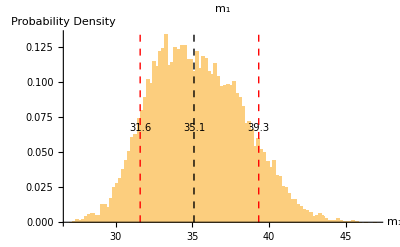

```mathematica
BCI["mass1"]=PlotParameterWithBCI[samples["mass1"],Subscript["m","1"]][[1]];
```

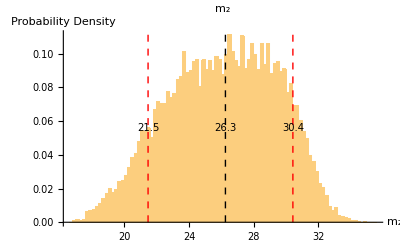

```mathematica
BCI["mass2"]=PlotParameterWithBCI[samples["mass2"],Subscript["m","2"]][[1]];
```

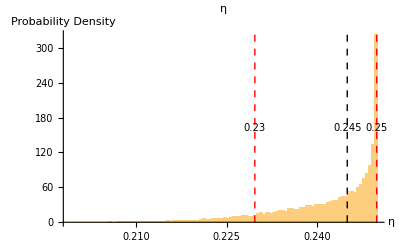

```mathematica
BCI["eta"]=PlotParameterWithBCI[samples["eta"],"η"][[1]];
```

### Plots Spin Components Aligning Orbital Angular Momentum (Then be it spin_z)

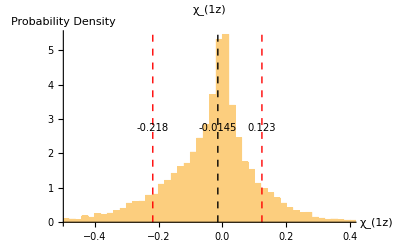

```mathematica
BCI["spin1_z"]=PlotParameterWithBCI[samples["spin1_z"],Subscript["χ","1z"]][[1]];
```

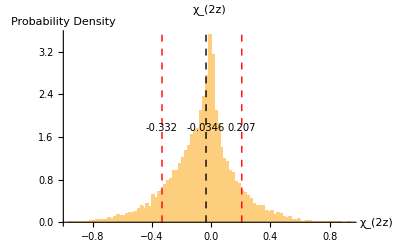

```mathematica
BCI["spin2_z"]=PlotParameterWithBCI[samples["spin2_z"],Subscript["χ","2z"]][[1]];
```

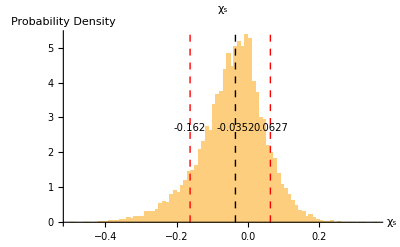

```mathematica
BCI["chis"]=PlotParameterWithBCI[samples["chis"],Subscript["χ","s"]][[1]];
```

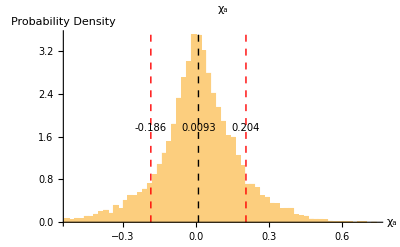

```mathematica
BCI["chia"]=PlotParameterWithBCI[samples["chia"],Subscript["χ","a"]][[1]];
```

### Plot N-Order Coefficients

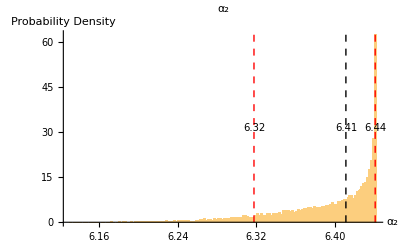

```mathematica
BCI["alpha2"]=PlotParameterWithBCI[samples["alpha2"],Subscript["α","2"]][[1]];
```

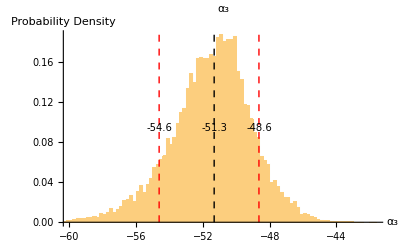

```mathematica
BCI["alpha3"]=PlotParameterWithBCI[samples["alpha3"],Subscript["α","3"]][[1]];
```

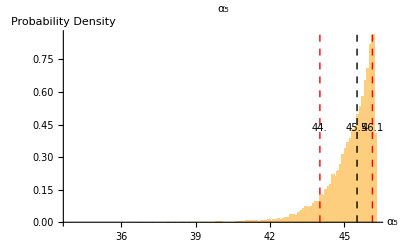

```mathematica
BCI["alpha5"]=PlotParameterWithBCI[samples["alpha4"],Subscript["α","5"]][[1]];
```

NumberForm::reqsigz: Requested number precision is lower than number of digits shown; padding with zeros.

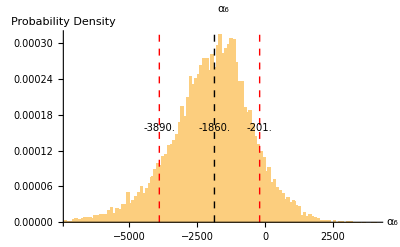

```mathematica
BCI["alpha6"]=PlotParameterWithBCI[samples["alpha6"],Subscript["α","6"]][[1]];
```

NumberForm::reqsigz: Requested number precision is lower than number of digits shown; padding with zeros.

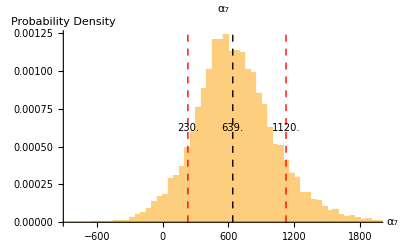

```mathematica
BCI["alpha7"]=PlotParameterWithBCI[samples["alpha7"],Subscript["α","7"]][[1]];
```

### Plot N-Order Log Coefficients

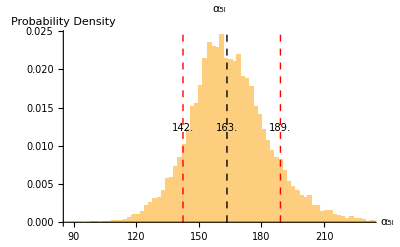

```mathematica
BCI["alpha5l"]=PlotParameterWithBCI[samples["alpha5l"],Subscript["α","5l"]][[1]];
```

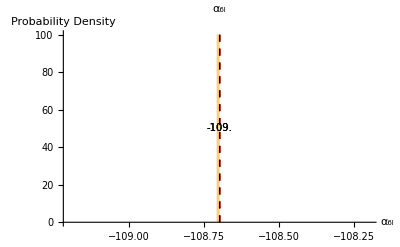

```mathematica
BCI["alpha6l"]=PlotParameterWithBCI[samples["alpha6l"],Subscript["α","6l"]][[1]];
```

NumberForm::reqsigz: Requested number precision is lower than number of digits shown; padding with zeros.

General::stop: Further output of NumberForm::reqsigz will be suppressed during this calculation.

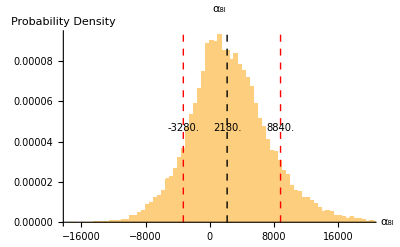

```mathematica
BCI["alpha8l"]=PlotParameterWithBCI[samples["alpha8l"],Subscript["α","8l"]][[1]];
```

### Plot psi

NumberForm::reqsigz: Requested number precision is lower than number of digits shown; padding with zeros.

General::stop: Further output of NumberForm::reqsigz will be suppressed during this calculation.

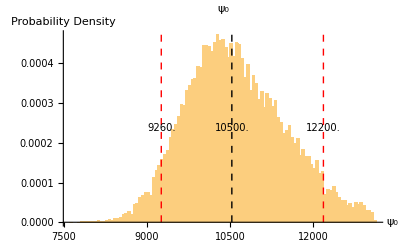

```mathematica
BCI["psi0"]=PlotParameterWithBCI[samples["psi0"],Subscript["ψ","0"]][[1]];
```

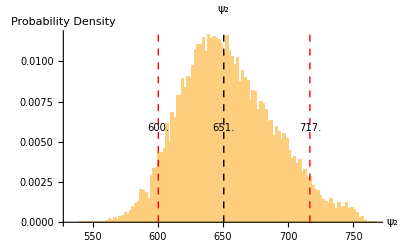

```mathematica
BCI["psi2"]=PlotParameterWithBCI[samples["psi2"],Subscript["ψ","2"]][[1]];
```

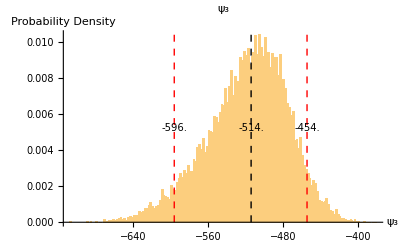

```mathematica
BCI["psi3"]=PlotParameterWithBCI[samples["psi3"],Subscript["ψ","3"]][[1]];
```

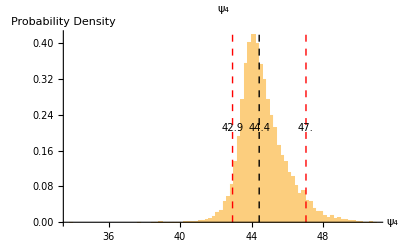

```mathematica
BCI["psi4"]=PlotParameterWithBCI[samples["psi4"],Subscript["ψ","4"]][[1]];
```

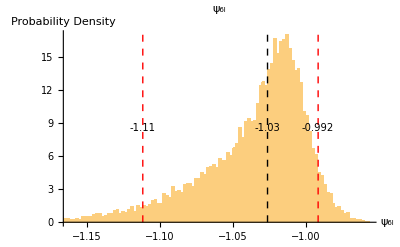

```mathematica
BCI["psi6l"]=PlotParameterWithBCI[samples["psi6l"],Subscript["ψ","6l"]][[1]];
```

### Plot Freedom-Released Coefficients

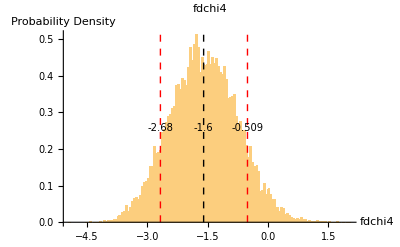

```mathematica
BCI[deviationName]=PlotParameterWithBCI[samples[deviationName],deviationName][[1]];
```

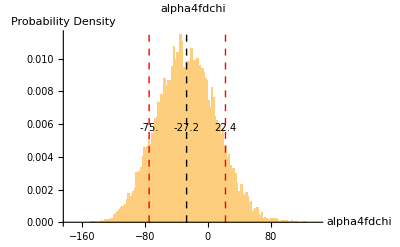

```mathematica
BCI[modifiedAlphaName]=PlotParameterWithBCI[samples[modifiedAlphaName],modifiedAlphaName][[1]];
```

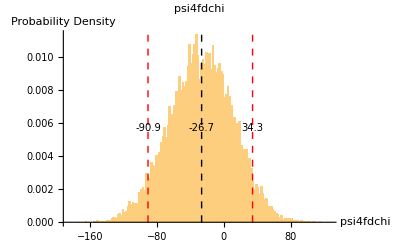

```mathematica
BCI[modifiedPsiName]=PlotParameterWithBCI[samples[modifiedPsiName],modifiedPsiName][[1]];
```

## Calculate Dots

### 2D, m_1-m_2, Fix two spin parameters

#### Set m_2-m_1 Axis

```mathematica
m2s=Range[BCI["mass2"][[1]],BCI["mass2"][[3]],0.1];
m1s=Range[BCI["mass1"][[1]],BCI["mass1"][[3]],0.1];
```

#### ψ_0 and ψ_2 Pancakes

```mathematica
pancakes=<||>
```

<||>

```mathematica
pancakes["psi0"]=HypersurfacePancake[Function[{l,m1,m2,χ1L,χ2L},Psi[l,η[m1,m2],M[m1,m2],χ1L,χ2L]],
BCI["psi0"],{m2s},{2},{0,BCI["spin1_z"][[2]],BCI["spin2_z"][[2]]},BCI["mass2"],2];
```

```mathematica
pancakes["psi2"]=HypersurfacePancake[Function[{l,m1,m2,χ1L,χ2L},Psi[l,η[m1,m2],M[m1,m2],χ1L,χ2L]],
BCI["psi2"],{m2s},{2},{2,BCI["spin1_z"][[2]],BCI["spin2_z"][[2]]},BCI["mass2"],2];
```

```mathematica
pancakes[psiName]=HypersurfacePancake[Function[{l,m1,m2,χ1L,χ2L},Psi[l,η[m1,m2],M[m1,m2],χ1L,χ2L]],
BCI[psiName],{m2s},{2},{deviationOrder,BCI["spin1_z"][[2]],BCI["spin2_z"][[2]]},BCI["mass2"],2];
```

FindRoot::lstol: The line search decreased the step size to within tolerance specified by AccuracyGoal and PrecisionGoal but was unable to find a sufficient decrease in the merit function. You may need more than MachinePrecision digits of working precision to meet these tolerances.

General::stop: Further output of FindRoot::lstol will be suppressed during this calculation.

General::munfl: 1/((68.2999-5.36517×10^-302 ⅈ)^4) is too small to represent as a normalized machine number; precision may be lost.

General::munfl: 0.000281113 (0.0251025+3.38079×10^-305 ⅈ) is too small to represent as a normalized machine number; precision may be lost.

General::munfl: 1/((67.1968+7.59298×10^-316 ⅈ)^4) is too small to represent as a normalized machine number; precision may be lost.

General::stop: Further output of General::munfl will be suppressed during this calculation.

#### ψ_0 and ψ_2 Non-GR Pancakes

```mathematica
pancakes[modifiedPsiName]=HypersurfacePancake[Function[{l,m1,m2,χ1L,χ2L},Psi[l,η[m1,m2],M[m1,m2],χ1L,χ2L]],
BCI[modifiedPsiName],{m2s},{2},{deviationOrder,BCI["spin1_z"][[2]],BCI["spin2_z"][[2]]},BCI["mass2"],2];
```

FindRoot::lstol: The line search decreased the step size to within tolerance specified by AccuracyGoal and PrecisionGoal but was unable to find a sufficient decrease in the merit function. You may need more than MachinePrecision digits of working precision to meet these tolerances.

General::stop: Further output of FindRoot::lstol will be suppressed during this calculation.

```mathematica
pancakes[psiName<>"1e-1"]=HypersurfacePancake[Function[{l,m1,m2,χ1L,χ2L},Psi[l,η[m1,m2],M[m1,m2],χ1L,χ2L]],
BCI[psiName](1+0.1),{m2s},{2},{deviationOrder,BCI["spin1_z"][[2]],BCI["spin2_z"][[2]]},BCI["mass2"],2];
```

FindRoot::lstol: The line search decreased the step size to within tolerance specified by AccuracyGoal and PrecisionGoal but was unable to find a sufficient decrease in the merit function. You may need more than MachinePrecision digits of working precision to meet these tolerances.

General::stop: Further output of FindRoot::lstol will be suppressed during this calculation.

General::munfl: 1/((49.1032+4.58105×10^-303 ⅈ)^4) is too small to represent as a normalized machine number; precision may be lost.

General::munfl: 0.000346933 (0.0384025-6.7559×10^-306 ⅈ) is too small to represent as a normalized machine number; precision may be lost.

General::munfl: 1/((49.0486+3.63793×10^-318 ⅈ)^4) is too small to represent as a normalized machine number; precision may be lost.

General::stop: Further output of General::munfl will be suppressed during this calculation.

```mathematica
pancakes[psiName<>"1e-2"]=HypersurfacePancake[Function[{l,m1,m2,χ1L,χ2L},Psi[l,η[m1,m2],M[m1,m2],χ1L,χ2L]],
BCI[psiName](1+0.01),{m2s},{2},{deviationOrder,BCI["spin1_z"][[2]],BCI["spin2_z"][[2]]},BCI["mass2"],2];
```

FindRoot::lstol: The line search decreased the step size to within tolerance specified by AccuracyGoal and PrecisionGoal but was unable to find a sufficient decrease in the merit function. You may need more than MachinePrecision digits of working precision to meet these tolerances.

General::stop: Further output of FindRoot::lstol will be suppressed during this calculation.

General::munfl: 1/((65.5175-6.22738×10^-316 ⅈ)^4) is too small to represent as a normalized machine number; precision may be lost.

General::munfl: 1/((65.3194+4.01605×10^-316 ⅈ)^4) is too small to represent as a normalized machine number; precision may be lost.

General::munfl: 1/((64.802+6.59152×10^-316 ⅈ)^4) is too small to represent as a normalized machine number; precision may be lost.

General::stop: Further output of General::munfl will be suppressed during this calculation.

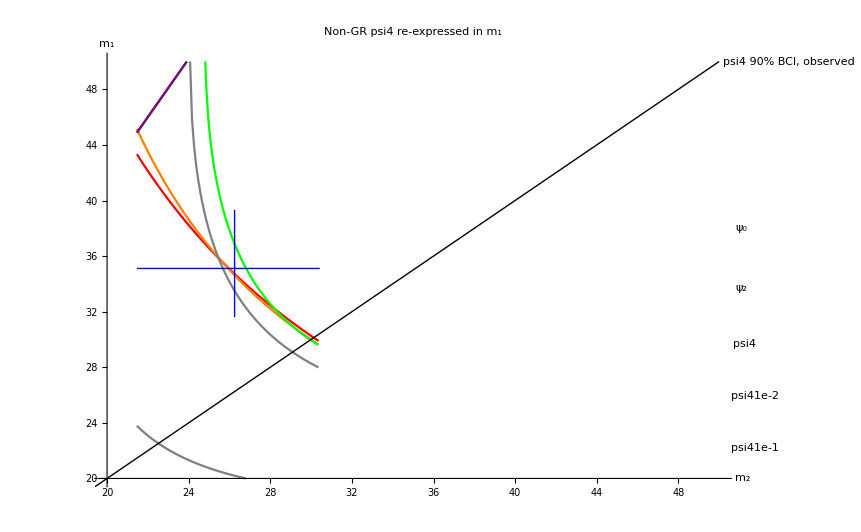

```mathematica
ListLinePlot[
{
Labeled[pancakes["psi0"][[2]][[2;;]],Subscript["ψ","0"]],
Labeled[pancakes["psi2"][[2]][[2;;]],Subscript["ψ","2"]],
Labeled[pancakes[psiName][[2]][[2;;]],psiName],

Labeled[pancakes[psiName<>"1e-2"][[2]][[2;;]],psiName<>"1e-2"],

Labeled[pancakes[psiName<>"1e-1"][[2]][[2;;]],psiName<>"1e-1"],

Labeled[pancakes[modifiedPsiName][[1]][[2;;]],psiName<>" 10% BCI, observed"],
Labeled[pancakes[modifiedPsiName][[2]][[2;;]],psiName<>" 50% BCI, observed"],
Labeled[pancakes[modifiedPsiName][[3]][[2;;]],psiName<>" 90% BCI, observed"]
},
PlotStyle->{Red,Orange,Green,Gray,Gray,Purple,Purple,Purple},
Epilog->{
Blue,Line[{{BCI["mass2"][[2]],BCI["mass1"][[1]]},{BCI["mass2"][[2]],BCI["mass1"][[3]]}}],
Blue,Line[{{BCI["mass2"][[1]],BCI["mass1"][[2]]},{BCI["mass2"][[3]],BCI["mass1"][[2]]}}],
Black,Line[{{0,0},{50,50}}]
	},
PlotLabel->"Non-GR "<>psiName<>" re-expressed in "Subscript["m","1"],
AxesLabel->{Subscript["m","2"],Subscript["m","1"]},
PlotRange->{{20,50},{20,50}}
]
```

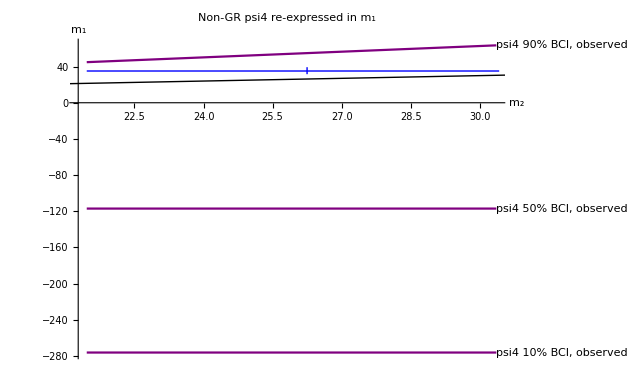

```mathematica
ListLinePlot[
{
Labeled[pancakes[modifiedPsiName][[1]][[2;;]],psiName<>" 10% BCI, observed"],
Labeled[pancakes[modifiedPsiName][[2]][[2;;]],psiName<>" 50% BCI, observed"],
Labeled[pancakes[modifiedPsiName][[3]][[2;;]],psiName<>" 90% BCI, observed"]
},
PlotStyle->{Purple},
Epilog->{
Blue,Line[{{BCI["mass2"][[2]],BCI["mass1"][[1]]},{BCI["mass2"][[2]],BCI["mass1"][[3]]}}],
Blue,Line[{{BCI["mass2"][[1]],BCI["mass1"][[2]]},{BCI["mass2"][[3]],BCI["mass1"][[2]]}}],
Black,Line[{{0,0},{50,50}}]
	},
PlotLabel->"Non-GR "<>psiName<>" re-expressed in "Subscript["m","1"],
AxesLabel->{Subscript["m","2"],Subscript["m","1"]}
]
```

#### ψ_0 and ψ_2 Pancakes, but over m_1-m_2 axis

```mathematica
(* FindRoot寻根，多值性的问题 *)
```

```mathematica
pancakesNew=<||>;
```

```mathematica
pancakesNew["psi0"]=HypersurfacePancake[Function[{l,m1,m2,χ1L,χ2L},Psi[l,η[m1,m2],M[m1,m2],χ1L,χ2L]],
BCI["psi0"],{m1s},{2},{0,BCI["spin1_z"][[2]],BCI["spin2_z"][[2]]},BCI["mass2"],3];
```

```mathematica
pancakesNew["psi2"]=HypersurfacePancake[Function[{l,m1,m2,χ1L,χ2L},Psi[l,η[m1,m2],M[m1,m2],χ1L,χ2L]],
BCI["psi2"],{m1s},{2},{2,BCI["spin1_z"][[2]],BCI["spin2_z"][[2]]},BCI["mass2"],3];
```

```mathematica
pancakesNew[psiName]=HypersurfacePancake[Function[{l,m1,m2,χ1L,χ2L},Psi[l,η[m1,m2],M[m1,m2],χ1L,χ2L]],
BCI[psiName],{m1s},{2},{deviationOrder,BCI["spin1_z"][[2]],BCI["spin2_z"][[2]]},BCI["mass2"],3];
```

#### ψ_0 and ψ_2 Non-GR Pancakes, but over m_1-m_2 axis

```mathematica
pancakesNew[modifiedPsiName]=HypersurfacePancake[Function[{l,m1,m2,χ1L,χ2L},Psi[l,η[m1,m2],M[m1,m2],χ1L,χ2L]],
BCI[modifiedPsiName],{m1s},{2},{deviationOrder,BCI["spin1_z"][[2]],BCI["spin2_z"][[2]]},BCI["mass2"],3];
```

FindRoot::lstol: The line search decreased the step size to within tolerance specified by AccuracyGoal and PrecisionGoal but was unable to find a sufficient decrease in the merit function. You may need more than MachinePrecision digits of working precision to meet these tolerances.

FindRoot::cvmit: Failed to converge to the requested accuracy or precision within 100 iterations.

FindRoot::lstol: The line search decreased the step size to within tolerance specified by AccuracyGoal and PrecisionGoal but was unable to find a sufficient decrease in the merit function. You may need more than MachinePrecision digits of working precision to meet these tolerances.

General::stop: Further output of FindRoot::lstol will be suppressed during this calculation.

```mathematica
pancakesNew[psiName<>"1e-1"]=HypersurfacePancake[Function[{l,m1,m2,χ1L,χ2L},Psi[l,η[m1,m2],M[m1,m2],χ1L,χ2L]],
BCI[psiName](1+0.1),{m1s},{2},{deviationOrder,BCI["spin1_z"][[2]],BCI["spin2_z"][[2]]},BCI["mass2"],3];
```

FindRoot::lstol: The line search decreased the step size to within tolerance specified by AccuracyGoal and PrecisionGoal but was unable to find a sufficient decrease in the merit function. You may need more than MachinePrecision digits of working precision to meet these tolerances.

General::stop: Further output of FindRoot::lstol will be suppressed during this calculation.

```mathematica
pancakesNew[psiName<>"1e-2"]=HypersurfacePancake[Function[{l,m1,m2,χ1L,χ2L},Psi[l,η[m1,m2],M[m1,m2],χ1L,χ2L]],
BCI[psiName](1+0.01),{m1s},{2},{deviationOrder,BCI["spin1_z"][[2]],BCI["spin2_z"][[2]]},BCI["mass2"],3];
```

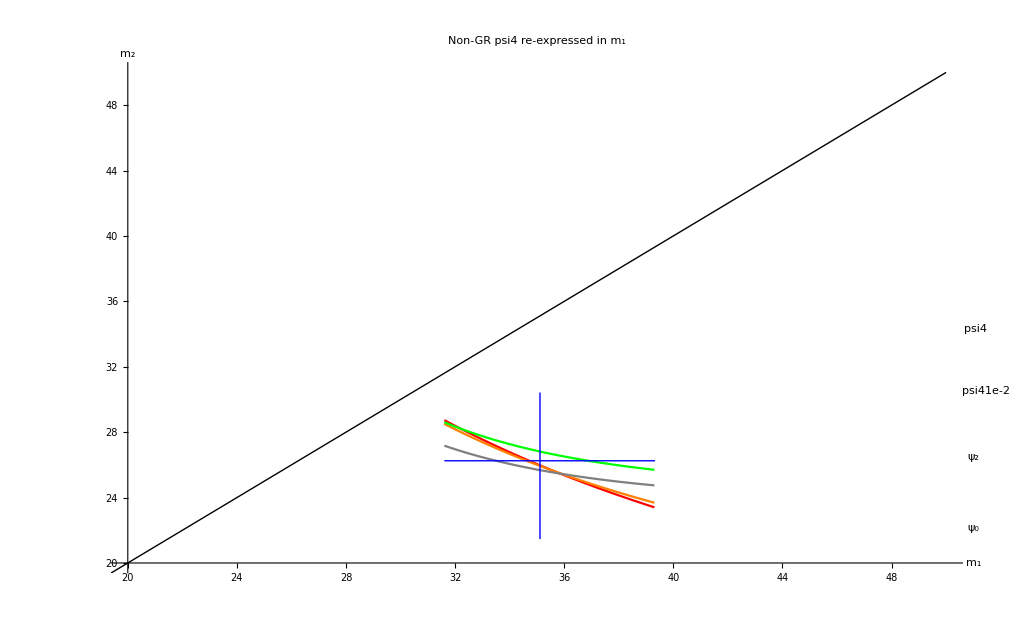

```mathematica
ListLinePlot[
{
Labeled[pancakesNew["psi0"][[2]][[2;;]],Subscript["ψ","0"]],
Labeled[pancakesNew["psi2"][[2]][[2;;]],Subscript["ψ","2"]],
Labeled[pancakesNew[psiName][[2]][[2;;]],psiName],

Labeled[pancakesNew[psiName<>"1e-2"][[2]][[2;;]],psiName<>"1e-2"],

Labeled[pancakesNew[psiName<>"1e-1"][[2]][[2;;]],psiName<>"1e-1"],

Labeled[pancakesNew[modifiedPsiName][[1]][[2;;]],psiName<>" 10% BCI, observed"],
Labeled[pancakesNew[modifiedPsiName][[2]][[2;;]],psiName<>" 50% BCI, observed"],
Labeled[pancakesNew[modifiedPsiName][[3]][[2;;]],psiName<>" 90% BCI, observed"]
},
PlotStyle->{Red,Orange,Green,Gray,Gray,Purple,Purple,Purple},
Epilog->{
Blue,Line[{{BCI["mass1"][[2]],BCI["mass2"][[1]]},{BCI["mass1"][[2]],BCI["mass2"][[3]]}}],
Blue,Line[{{BCI["mass1"][[1]],BCI["mass2"][[2]]},{BCI["mass1"][[3]],BCI["mass2"][[2]]}}],
Black,Line[{{0,0},{50,50}}]
	},
PlotLabel->"Non-GR "<>psiName<>" re-expressed in "Subscript["m","1"],
AxesLabel->{Subscript["m","1"],Subscript["m","2"]},
PlotRange->{{20,50},{20,50}}
]
```

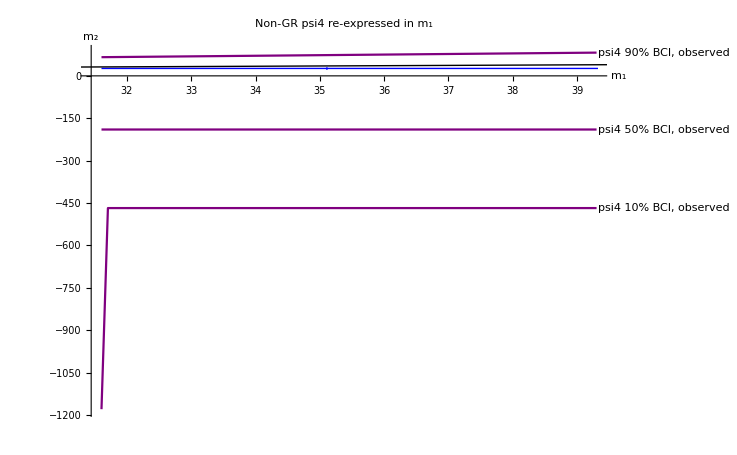

```mathematica
ListLinePlot[
{
Labeled[pancakesNew[modifiedPsiName][[1]][[2;;]],psiName<>" 10% BCI, observed"],
Labeled[pancakesNew[modifiedPsiName][[2]][[2;;]],psiName<>" 50% BCI, observed"],
Labeled[pancakesNew[modifiedPsiName][[3]][[2;;]],psiName<>" 90% BCI, observed"]
},
PlotStyle->{Purple},
Epilog->{
Blue,Line[{{BCI["mass1"][[2]],BCI["mass2"][[1]]},{BCI["mass1"][[2]],BCI["mass2"][[3]]}}],
Blue,Line[{{BCI["mass1"][[1]],BCI["mass2"][[2]]},{BCI["mass1"][[3]],BCI["mass2"][[2]]}}],
Black,Line[{{0,0},{50,50}}]
	},
PlotLabel->"Non-GR "<>psiName<>" re-expressed in "Subscript["m","1"],
AxesLabel->{Subscript["m","1"],Subscript["m","2"]}
]
```

### 3D, χ_s-χ_a-η

```mathematica
chiss=Range[BCI["chis"][[1]],BCI["chis"][[2]],1/50];
chias=Range[BCI["chia"][[1]],BCI["chia"][[2]],1/50];
```

```mathematica
pancakes[alphaName]=HypersurfacePancake[
Function[{j,eta,chis,chia},
Alpha[j,eta,χ1L[chis,chia],χ2L[chis,chia]]],(* F_ *)
BCI[alphaName],(* F0_ *)
{chiss,chias},{2,3},(* axes_,axesIndices_ *)
{deviationOrder},(* FArgs_ *)
BCI["eta"],2(* h0_,hIndex_ *)
];
```

FindRoot::cvmit: Failed to converge to the requested accuracy or precision within 100 iterations.

General::stop: Further output of FindRoot::cvmit will be suppressed during this calculation.

FindRoot::lstol: The line search decreased the step size to within tolerance specified by AccuracyGoal and PrecisionGoal but was unable to find a sufficient decrease in the merit function. You may need more than MachinePrecision digits of working precision to meet these tolerances.

General::stop: Further output of FindRoot::lstol will be suppressed during this calculation.

```mathematica
Select[Flatten[pancakes[alphaName][[1]],Depth=1],Im[#[[3]]]==0 &];
```

Set::wrsym: Symbol Depth is Protected.

```mathematica
ListPlot3D[
{
Select[Flatten[pancakes[alphaName][[1]],Depth=1],Im[#[[3]]]==0 &]
(*,Select[Flatten[pancakes[alphaName][[2]],Depth=1],Im[#[[3]]]==0 &]*)
(*,Select[Flatten[pancakes[alphaName][[3]],Depth=1],Im[#[[3]]]==0 &]*)
},
PlotRange->{{BCI["chis"][[1]],BCI["chis"][[3]]},{BCI["chia"][[1]],BCI["chia"][[3]]},{BCI["eta"][[1]],BCI["eta"][[3]]}}
]
```

Set::wrsym: Symbol Depth is Protected.

-Graphics3D-

```mathematica
pancakesFixChia[alphaName]=HypersurfacePancake[
Function[{j,eta,chis,chia},
Alpha[j,eta,χ1L[chis,chia],χ2L[chis,chia]]],(* F_ *)
BCI[alphaName],(* F0_ *)
{chiss},{2},(* axes_,axesIndices_ *)
{deviationOrder,BCI["chia"][[2]]},(* FArgs_ *)
BCI["eta"],2(* h0_,hIndex_ *)
];
```

FindRoot::cvmit: Failed to converge to the requested accuracy or precision within 100 iterations.

FindRoot::lstol: The line search decreased the step size to within tolerance specified by AccuracyGoal and PrecisionGoal but was unable to find a sufficient decrease in the merit function. You may need more than MachinePrecision digits of working precision to meet these tolerances.

General::stop: Further output of FindRoot::lstol will be suppressed during this calculation.

FindRoot::cvmit: Failed to converge to the requested accuracy or precision within 100 iterations.

```mathematica
pancakesFixChia[modifiedAlphaName]=HypersurfacePancake[
Function[{j,eta,chis,chia},
Alpha[j,eta,χ1L[chis,chia],χ2L[chis,chia]]],(* F_ *)
BCI[modifiedAlphaName],(* F0_ *)
{chiss},{2},(* axes_,axesIndices_ *)
{deviationOrder,BCI["chia"][[2]]},(* FArgs_ *)
BCI["eta"],2(* h0_,hIndex_ *)
];
```

FindRoot::lstol: The line search decreased the step size to within tolerance specified by AccuracyGoal and PrecisionGoal but was unable to find a sufficient decrease in the merit function. You may need more than MachinePrecision digits of working precision to meet these tolerances.

General::stop: Further output of FindRoot::lstol will be suppressed during this calculation.

```mathematica
pancakesFixChia[modifiedAlphaName]
```

{{{-0.176261,-2.23601},{-0.156261,-2.63373},{-0.136261,-3.13345},{-0.116261,-3.78142},{-0.0962614,-4.65754},{-0.0762614,-5.91358},{-0.0562614,-7.88009}},{{-0.176261,-0.515673},{-0.156261,-0.705506},{-0.136261,-0.942205},{-0.116261,-1.24574},{-0.0962614,-1.64989},{-0.0762614,-2.21694},{-0.0562614,-3.07708}},{{-0.176261,0.287298+3.5425×10^-15 ⅈ},{-0.156261,0.280539+2.72387×10^-15 ⅈ},{-0.136261,0.273704+3.80329×10^-15 ⅈ},{-0.116261,0.26679+2.26418×10^-15 ⅈ},{-0.0962614,0.259798+3.88682×10^-15 ⅈ},{-0.0762614,0.252725+1.98253×10^-15 ⅈ},{-0.0562614,0.22858}}}

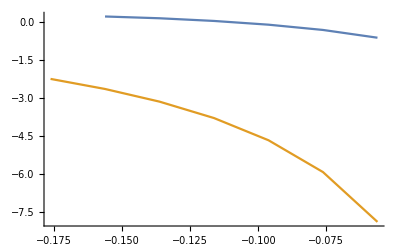

```mathematica
ListLinePlot[
{
Select[pancakesFixChia[alphaName][[1]],Im[#[[2]]]==0 &],
Select[pancakesFixChia[modifiedAlphaName][[1]],Im[#[[2]]]==0 &],
Select[pancakesFixChia[modifiedAlphaName][[3]],Im[#[[2]]]==0 &]
}
(*,PlotRange->{{-0.3,0},{0,1/4}}*)
]
```